```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
leads[z_]:=leads[z]=Table[ToExpression[Import["~/Downloads/mostimp/PhD_new/PhD/fwi/AGNR/leads/size_"<>ToString[z]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2,0.01]}]
```

```mathematica
leads[3]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=leads[m][[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,117366]; J=J]*)
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
LEFT[0.66,0.0001,1,0,21]//AbsoluteTiming
```

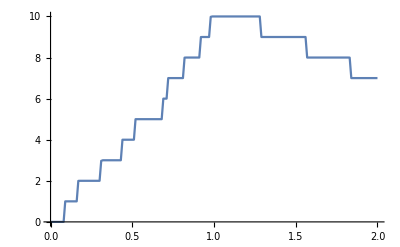

```mathematica
Table[{ω,tr[ω,0.0001,1,0,21]},{ω,Range[0,2,0.01]}]//ListLinePlot
```

```mathematica
Join[Table[{y,1},{y,100}],Table[{y,2},{y,100}],Table[{y,41},{y,100}],Table[{y,42},{y,100}]]//ListPlot
```

```mathematica
dist[number_,size_]:=dist[number,size]=Table[RandomSample[Flatten[Table[{x,y},{x,10},{y,size}],1],number],1000]
```

```mathematica
Total[Abs[7-Transpose[dist[2,7][[1]]][[2]]]]
```

3

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,size_,unitcell_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,size],abc=dist[concentration,size][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]]
```

```mathematica
f[1,1,1,0,1,3,1,1,1]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_,m_]:= Module[{},
recurs=Module[{J1= LEFT[ω,0.0001,1,0,m]},
Do[
J1=Inverse[IdentityMatrix[2m]-f[ω,0.0001,1,0,ϵ1,m,unitcell,concentration,number].ConjugateTranspose[T1[1,m]].J1.T1[1,m]].f[ω,0.0001,1,0,ϵ1,m,unitcell,concentration,number],{unitcell,10}];J1];ir=Inverse[IdentityMatrix[2m]-LEFT[ω,0.0001,1,0,m].ρ[1,m].recurs.ρ[1,m]].LEFT[ω,0.0001,1,0,m];il=Inverse[IdentityMatrix[2m]-recurs.ρ[1,m].LEFT[ω,0.0001,1,0,m].ρ[1,m]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.ρ[1,m].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[T[1,10]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];If[TRA>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],TRA]]
```

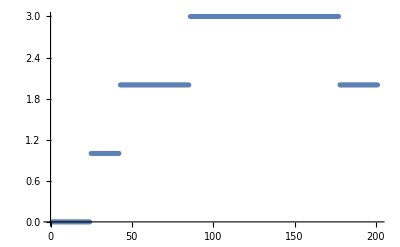

```mathematica
Monitor[Table[CA[w,0.0001,1,0,0,10,1,7],{w,Range[0,2,0.01]}],w]//ListPlot
```

```mathematica
Table[Table[Total[Abs[7-Transpose[dist[conc,7][[number]]][[2]]]],{number,1000}],{conc,15}]
```

```mathematica
%33[[2]]
```

{3,9,2,4,0,10,5,9,7,7,6,4,8,6,7,7,10,4,5,2,11,11,8,9,5,0,8,1,10,7,9,4,6,3,6,9,2,0,3,1,5,3,12,7,5,7,11,2,10,9,8,6,3,8,1,4,7,10,6,4,7,6,6,4,8,7,9,10,10,9,7,8,11,8,2,8,1,5,9,6,7,3,10,4,1,7,8,1,6,6,5,0,3,5,10,2,2,10,11,0,7,10,10,8,5,5,12,4,7,3,10,10,4,1,6,9,11,3,5,9,4,3,1,8,6,3,6,1,6,6,8,2,8,6,4,7,5,7,7,9,10,2,6,5,8,8,5,2,4,9,7,7,5,4,11,6,8,1,5,4,2,6,8,3,5,4,7,8,5,7,9,7,11,1,3,9,8,8,10,11,3,7,5,5,6,10,1,3,8,8,7,7,4,6,11,5,7,5,4,6,9,9,3,4,7,3,6,10,4,4,0,7,4,7,5,6,6,5,5,9,7,2,7,10,5,6,7,4,5,7,5,4,4,6,3,8,11,6,8,11,8,2,7,8,7,8,4,7,6,4,5,4,7,7,3,5,5,0,7,9,9,2,6,7,2,5,9,5,3,12,4,5,1,2,9,4,11,2,6,5,5,7,9,8,8,7,6,2,7,5,10,9,4,9,7,10,4,7,9,5,5,7,5,2,1,7,2,7,5,2,4,3,3,0,5,10,6,8,2,0,5,11,2,10,3,6,9,7,7,5,9,9,8,8,11,4,3,3,7,7,5,7,11,10,11,8,6,9,3,3,0,3,9,6,4,9,4,8,5,12,8,6,2,5,10,5,4,3,8,8,8,7,8,9,8,2,7,7,7,6,8,6,5,0,3,7,1,7,0,8,4,0,2,6,5,8,1,9,9,9,5,2,7,7,8,7,6,3,8,4,8,3,6,9,2,7,11,5,6,10,6,8,11,10,3,6,7,9,5,4,5,7,10,0,6,5,6,4,10,9,3,6,4,5,7,11,5,3,3,4,7,10,9,7,2,4,11,6,4,10,6,5,3,4,7,7,6,10,5,8,6,4,3,11,2,5,6,9,1,9,6,3,3,7,7,9,4,6,8,1,1,9,6,3,2,1,9,2,1,8,3,8,3,9,7,7,6,4,5,8,6,3,8,7,6,1,2,9,8,6,6,12,6,11,4,4,8,1,9,8,2,9,9,2,2,8,5,6,8,3,4,5,5,6,7,0,1,3,5,3,10,8,1,7,4,8,5,6,1,11,6,4,4,7,9,8,8,12,5,3,11,7,8,5,1,2,9,8,9,8,2,4,5,4,10,5,8,10,1,4,4,7,7,7,3,7,5,6,8,10,0,3,7,11,8,2,7,8,4,4,6,7,6,6,10,4,7,10,6,9,8,6,4,3,8,1,4,6,4,3,6,5,11,6,9,5,6,4,3,6,6,10,7,3,8,9,7,5,8,6,9,9,4,6,1,2,4,7,4,2,11,6,3,3,7,6,4,5,7,9,9,4,8,2,5,10,1,10,1,4,1,7,2,3,6,6,1,5,5,6,8,4,7,6,8,3,4,8,1,7,5,8,9,8,2,9,11,11,11,6,12,3,3,10,4,4,7,12,5,5,1,9,3,5,6,4,5,10,11,8,7,7,5,1,10,4,2,4,4,8,2,4,3,7,7,9,8,0,6,3,9,8,6,3,12,9,10,11,2,4,6,3,11,12,3,3,6,8,7,2,5,6,2,6,11,8,9,5,3,10,6,1,6,5,8,6,1,12,3,1,1,9,8,11,5,5,5,5,6,6,2,1,6,9,8,6,2,0,6,7,4,5,8,6,8,7,8,6,2,8,1,7,5,8,11,9,4,2,6,6,6,10,6,6,9,9,2,8,6,10,10,9,9,10,5,7,3,6,6,8,8,11,6,6,8,12,8,7,1,1,7,5,4,10,6,7,10,4,3,9,6,6,2,4,4,9,5,6,11,7,8,11,3,7,3,0,2,7,8,4,1,3,8,7,8,7,11,8,8,6,9,7,2,5,5,8,4,7,3,12,9,1,9,9,4,7,2,7,6,5,7,7,6,9,5,1,6,6,10,9,12,7,8,1,8,4,3,6,5,11,7,6,7,5,3,1,4,6,5,8,4,7,7,0,8,4,11,3,6,1,12,5,5,7,4,8,7,8,10,5,4,7,7,5,10,2,10,7,10,6,5,3,2,3,5,2,5,3,11,0,5,7,6,6,5,5,4,9,2,3}

```mathematica
Total[Abs[7-Transpose[dist[15,7][[1000]]][[2]]]]
```

45

```mathematica
Monitor[Table[ParallelTable[{Total[Abs[7-Transpose[dist[conc,7][[num]]][[2]]]],CA[1.1,0.0001,1,0,0.5,conc,num,7]},{num,1000}],{conc,15}],conc]
```

```mathematica
SortBy[Flatten[%37,1],First]
```

```mathematica
Dimensions[%46][[1]]
```

15000

```mathematica
g1[m_]:=Module[{J={}},Do[If[%41[[x,1]]==m,AppendTo[J,%41[[x,2]]]],{x,Dimensions[%46][[1]]}];J]
```

```mathematica
Table[{x,Mean[g1[x]]},{x,Range[0,63,1]}]
```

{{0,2.60152},{1,2.78854},{2,2.5868},{3,2.6771},{4,2.53829},{5,2.63385},{6,2.50146},{7,2.4158},{8,2.35178},{9,2.35391},{10,2.27968},{11,2.26596},{12,2.22042},{13,2.11561},{14,2.11881},{15,2.07012},{16,2.02089},{17,1.99587},{18,2.01809},{19,1.95148},{20,1.90953},{21,1.8921},{22,1.8659},{23,1.80517},{24,1.78864},{25,1.7563},{26,1.72833},{27,1.77086},{28,1.71401},{29,1.66051},{30,1.64067},{31,1.63456},{32,1.68378},{33,1.62558},{34,1.57394},{35,1.59613},{36,1.56046},{37,1.56984},{38,1.55688},{39,1.53098},{40,1.53417},{41,1.53196},{42,1.4865},{43,1.52713},{44,1.49281},{45,1.48263},{46,1.45281},{47,1.43965},{48,1.46244},{49,1.52642},{50,1.47974},{51,1.40153},{52,1.40933},{53,1.37959},{54,1.40331},{55,1.38738},{56,1.40273},{57,1.40907},{58,1.58761},{59,1.37356},{60,1.52294},{61,1.3152},{62,1.29081},{63,1.76609}}

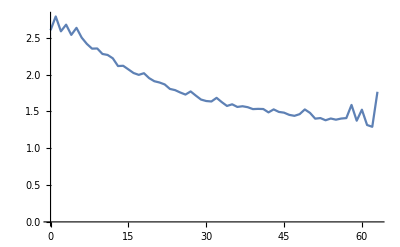

```mathematica
ListPlot[%54,Joined->True]
```

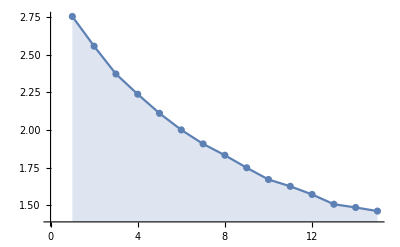

```mathematica
ListPlot[%76,Filling->Axis,Mesh->All,Joined->True]
```

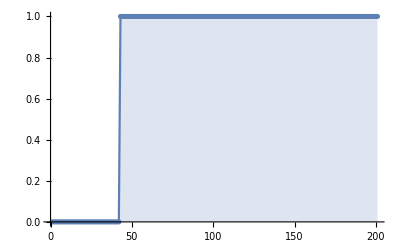

```mathematica
ListPlot[%71,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
Monitor[Table[{x,Abs[50-2x],Mean[ParallelTable[CA[1.1,0.0001,1,0,0.5,50,x,n,21],{n,1000}]]},{x,5,35,5}],x]
```

{{5,40,8.97695},{10,30,9.01436},{15,20,8.9852},{20,10,8.99203},{25,0,8.96767},{30,10,8.99231},{35,20,8.97735}}

```mathematica
ListLinePlot[ParallelTable[CA[ω,0.0001,1,0,0.5,50,25,1,21],{ω,Range[0,2,0.01]}]]
```

-Graphics-

```mathematica
d1[ω_,δ_,t_,ϵ_]:=d1[ω,δ,t,ϵ]=Module[{J=Inverse[(ω+ⅈ*δ-ϵ)IdentityMatrix[1]],B:=Inverse[(ω+ⅈ*δ-ϵ)IdentityMatrix[1]],T=t*IdentityMatrix[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,50000];J=J]
```

```mathematica
d1[0,0.0001,1,0]
```

{{0.-1.01351 ⅈ}}

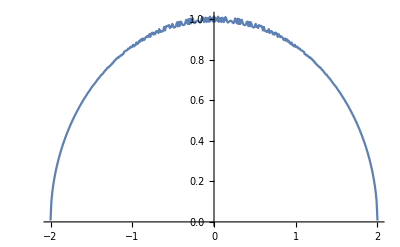

```mathematica
Show[ListLinePlot[Table[{ω,-Im[d1[ω,0.0001,1,0][[1,1]]]},{ω,Range[-2,2,0.01]}]]]
```

```mathematica
β[ω_,δ_,t_,ϵ_,γ_]:=
β[ω,δ,t,ϵ,γ]=ReplacePart[(ω+ⅈ*δ-ϵ-γ*Im[d1[ω,δ,t,ϵ][[1,1]]])IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
(*Import leads *)
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,γ_]:=LEFT[ω,δ,t,ϵ,γ]=(*Module[{J=Inverse[β[ω,δ,t,ϵ,γ]],B:=Inverse[β[ω,δ,t,ϵ,γ]],T=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.T.J.T].B,5000];J=J]*)Lead[[ω*100+1]]
```

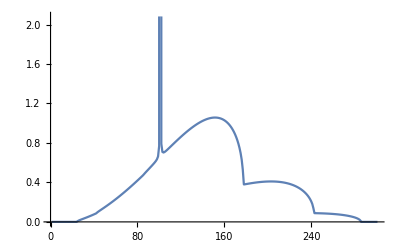

```mathematica
ListLinePlot[Monitor[Table[-Im[LEFT[ω,0.0001,1,0,0.1][[1,1]]],{ω,0,3,0.01}],ω]]
```

```mathematica
(*Or Generate leads using recursive algorithm*)
```

```mathematica
g[ω_,δ_,t_,ϵ_,γ_]:= Inverse[β[ω,δ,t,ϵ,γ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ,γ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ,γ].T1[t]].g[ω,δ,t,ϵ,γ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ,γ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ,γ].T1[t]].g[ω,δ,t,ϵ,γ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ,γ].TT[t].SR[ω,δ,t,ϵ,γ].TT[t]].SL[ω,δ,t,ϵ,γ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ,γ].TT[t].SL[ω,δ,t,ϵ,γ].TT[t]].SR[ω,δ,t,ϵ,γ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,γ_]:= IL[ω,δ,t,ϵ,γ]-ConjugateTranspose[IL[ω,δ,t,ϵ,γ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,γ_]:= IR[ω,δ,t,ϵ,γ]-ConjugateTranspose[IR[ω,δ,t,ϵ,γ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,γ_]:= SR[ω,δ,t,ϵ,γ].TT[t].IL[ω,δ,t,ϵ,γ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,γ_]:= Gnonlocal[ω,δ,t,ϵ,γ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,γ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,γ_]:=Abs[Tr[gdd[ω,δ,t,ϵ,γ].TT[t].grr[ω,δ,t,ϵ,γ].TT[t]-TT[t].GNON[ω,δ,t,ϵ,γ].TT[t].GNON[ω,δ,t,ϵ,γ]]]
```

```mathematica
tr[1,0.0001,1,0,0.01]
```

2.99917

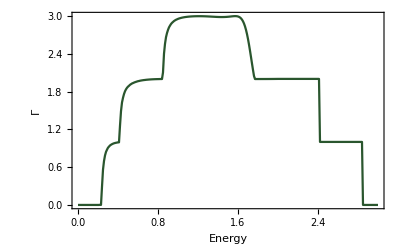

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0,0.1]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,14](*,s[38,50,38,50]*)],concentration]],First],10000]
```

```mathematica
dist[100,50][[1]]//Dimensions
```

{50,2}

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,γ_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,γ],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,γ_,total_,top_,number_,m_]:= Module[{},
recurs=Module[{J1= LEFT[ω,0.0001,1,0,γ]},
Do[
J1=Inverse[IdentityMatrix[2m]-f[ω,0.0001,1,0,ϵ1,γ,unitcell,total,top,number].ConjugateTranspose[T1[1]].J1.T1[1]].f[ω,0.0001,1,0,ϵ1,γ,unitcell,total,top,number],{unitcell,100}];J1];ir=Inverse[IdentityMatrix[2m]-LEFT[ω,0.0001,1,0,γ].ρ[1,m].recurs.ρ[1,m]].LEFT[ω,0.0001,1,0,γ];il=Inverse[IdentityMatrix[2m]-recurs.ρ[1,m].LEFT[ω,0.0001,1,0,γ].ρ[1,m]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.ρ[1,m].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[T[1,10]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];If[TRA>tr[ω,0.0001,1,0,γ],tr[ω,0.0001,1,0,γ],TRA]]
```

```mathematica
input=Monitor[Table[Monitor[Table[{ω,CA[ω,0.0001,1,0,0.5,0,100,25,num,7]},{ω,Range[0,3,0.01]}],ω],{num,10}],num]
```

{{{0.,2.8×10^-7},{0.01,2.78756×10^-7},{0.02,2.74967×10^-7},{0.03,2.68492×10^-7},{0.04,2.58829×10^-7},{0.05,2.45167×10^-7},{0.06,2.26296×10^-7},{0.07,2.00455×10^-7},{0.08,1.65118×10^-7},{0.09,1.16639×10^-7},{0.1,4.97186×10^-8},{0.11,4.34593×10^-8},{0.12,1.74632×10^-7},276,{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},8,{1}}
 |  |  |  |

```mathematica
input=Monitor[Table[Monitor[Table[{ω,CA[ω,0.0001,1,0,0.5,0.1,100,25,num,7]},{ω,Range[0,3,0.01]}],ω],{num,10}],num]
```

{{{0.,9.48896×10^-8},{0.01,1.78575×10^-7},{0.02,3.24021×10^-7},{0.03,3.38147×10^-7},{0.04,3.55295×10^-7},{0.05,3.79488×10^-7},{0.06,4.02892×10^-7},{0.07,4.38708×10^-7},{0.08,4.79726×10^-7},{0.09,5.26425×10^-7},{0.1,5.98349×10^-7},{0.11,6.833×10^-7},{0.12,7.86543×10^-7},276,{2.89,1.36405×10^-6},{2.9,8.87779×10^-7},{2.91,6.22925×10^-7},{2.92,4.60773×10^-7},{2.93,3.54426×10^-7},{2.94,2.80972×10^-7},{2.95,2.28145×10^-7},{2.96,1.88902×10^-7},{2.97,1.58963×10^-7},{2.98,1.35608×10^-7},{2.99,1.17042×10^-7},{3.,1.02041×10^-7}},8,{1}}
 |  |  |  |

```mathematica
transmission= Table[{X,Import["~/PhD_new/PhD/substrate_ca_7agnr_"<>ToString[X]<>"_.dat"]},{X,5,80,10}]
```

{{5,{{0.,2.96509×10^-7},{0.01,3.0547×10^-7},{0.02,3.20997×10^-7},{0.03,3.3342×10^-7},{0.04,3.50902×10^-7},{0.05,3.77331×10^-7},{0.06,3.99113×10^-7},{0.07,4.36477×10^-7},{0.08,4.75573×10^-7},{0.09,5.23361×10^-7},{0.1,5.96149×10^-7},{0.11,6.81341×10^-7},{0.12,7.84318×10^-7},276,{2.89,1.34745×10^-6},{2.9,8.76135×10^-7},{2.91,6.12682×10^-7},{2.92,4.56339×10^-7},{2.93,3.51105×10^-7},{2.94,2.79685×10^-7},{2.95,2.27142×10^-7},{2.96,1.88153×10^-7},{2.97,1.57922×10^-7},{2.98,1.3512×10^-7},{2.99,1.1623×10^-7},{3.,1.01332×10^-7}}},6,{75,1}}
 |  |  |  |

```mathematica
transmission100 = Table[{X,Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"]},{X,Range[5,85,2]}]
```

{{5,{{0.,2.79841×10^-7},{0.01,2.72438×10^-7},{0.02,2.76055×10^-7},{0.03,2.8154×10^-7},{0.04,2.86312×10^-7},{0.05,2.93608×10^-7},{0.06,3.05841×10^-7},{0.07,3.15627×10^-7},{0.08,3.3353×10^-7},{0.09,3.50681×10^-7},{0.1,3.75537×10^-7},{0.11,4.07619×10^-7},277,{2.89,1.34213×10^-6},{2.9,8.74763×10^-7},{2.91,6.1618×10^-7},{2.92,4.55387×10^-7},{2.93,3.50822×10^-7},{2.94,2.79217×10^-7},{2.95,2.26938×10^-7},{2.96,1.88087×10^-7},{2.97,1.58019×10^-7},{2.98,1.34547×10^-7},{2.99,1.15807×10^-7},{3.,1.01074×10^-7}}},{7,{1}},37,1,{85,{1}}}
 |  |  |  |

```mathematica
Dimensions[transmission100]
```

{41,2}

```mathematica
Misfit[x_,y_,n_]:=Module[{m5 = %119[[n]]},ρ1:= Table[{transmission100[[ξ,1]]/10,Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-transmission100[[ξ,2]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{ξ,41}]; 
ρ1]
```

```mathematica
Misfit[2.9,0,4]
```

{{5,0.660193},{7,0.5079},{9,0.39612},{11,0.313274},{13,0.250851},{15,0.203987},{17,0.169035},{19,0.143933},{21,0.125937},{23,0.113514},{25,0.105698},{27,0.1021},{29,0.102769},{31,0.104618},{33,0.109005},{35,0.115852},{37,0.123011},{39,0.131197},{41,0.141084},{43,0.152049},{45,0.16353},{47,0.173644},{49,0.185119},{51,0.196522},{53,0.20967},{55,0.221143},{57,0.233094},{59,0.244179},{61,0.256732},{63,0.268009},{65,0.280129},{67,0.29092},{69,0.301502},{71,0.313247},{73,0.323205},{75,0.33257},{77,0.344415},{79,0.353158},{81,0.36474},{83,0.37326},{85,0.382194}}

```mathematica
Transpose[%1][[2]]
```

{0.660193,0.5079,0.39612,0.313274,0.250851,0.203987,0.169035,0.143933,0.125937,0.113514,0.105698,0.1021,0.102769,0.104618,0.109005,0.115852,0.123011,0.131197,0.141084,0.152049,0.16353,0.173644,0.185119,0.196522,0.20967,0.221143,0.233094,0.244179,0.256732,0.268009,0.280129,0.29092,0.301502,0.313247,0.323205,0.33257,0.344415,0.353158,0.36474,0.37326,0.382194}

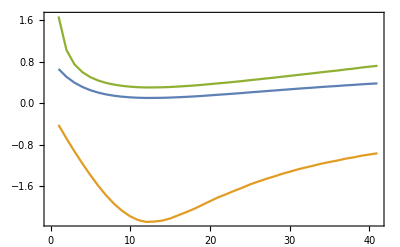

```mathematica
ListPlot[{%4,Log[Transpose[%1][[2]]],Log[Transpose[%1][[2]],0.5]},Joined->True,Frame->True]
```

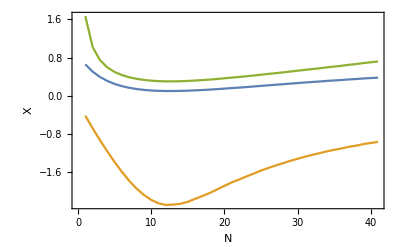

```mathematica
Show[%15,FrameLabel->{{HoldForm[Χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}]
```

```mathematica
Table[{x,Interpolation[Misfit[2.9,0,4]][x]},{x,Range[1,8,0.2]}]
```

{{1.,0.570284},{1.2,0.451331},{1.4,0.353717},{1.6,0.275449},{1.8,0.214537},{2.,0.168987},{2.2,0.136808},{2.4,0.116007},{2.6,0.104592},{2.8,0.100571},{3.,0.101953},{3.2,0.100707},{3.4,0.102389},{3.6,0.106515},{3.8,0.112601},{4.,0.120166},{4.2,0.127349},{4.4,0.135388},{4.6,0.144146},{4.8,0.153485},{5.,0.163266},{5.2,0.173166},{5.4,0.183279},{5.6,0.19351},{5.8,0.203767},{6.,0.213959},{6.2,0.223623},{6.4,0.233129},{6.6,0.242476},{6.8,0.251666},{7.,0.260698},{7.2,0.269571},{7.4,0.278288},{7.6,0.286846},{7.8,0.295247},{8.,0.30349}}

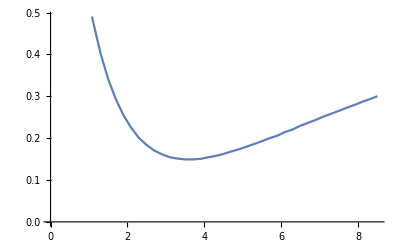

```mathematica
ListPlot[%179,Joined->True]
```

```mathematica
%196
```

{{1.,0.570284},{1.2,0.451331},{1.4,0.353717},{1.6,0.275449},{1.8,0.214537},{2.,0.168987},{2.2,0.136808},{2.4,0.116007},{2.6,0.104592},{2.8,0.100571},{3.,0.101953},{3.2,0.100707},{3.4,0.102389},{3.6,0.106515},{3.8,0.112601},{4.,0.120166},{4.2,0.127349},{4.4,0.135388},{4.6,0.144146},{4.8,0.153485},{5.,0.163266},{5.2,0.173166},{5.4,0.183279},{5.6,0.19351},{5.8,0.203767},{6.,0.213959},{6.2,0.223623},{6.4,0.233129},{6.6,0.242476},{6.8,0.251666},{7.,0.260698},{7.2,0.269571},{7.4,0.278288},{7.6,0.286846},{7.8,0.295247},{8.,0.30349}}

```mathematica
Export["~/PhD_new/PhD/misfit_subs.dat",%196]
```

~/PhD_new/PhD/misfit_subs.dat

```mathematica
l[n_]:=Misfit[2.9,0,n][[Position[Misfit[2.9,0,n],Min[Misfit[2.9,0,n]]][[1,1]]]]
```

```mathematica
Table[l[n],{n,10}]
```

{{3,0.131677},{3,0.0985957},{3,0.108348},{3,0.101953},{3,0.111919},{3,0.165842},{3,0.139958},{3,0.131622},{3,0.138789},{3,0.119455}}

```mathematica
Misfit[2.9,0,4]
```

{{1/2,0.660193},{7/10,0.5079},{9/10,0.39612},{11/10,0.313274},{13/10,0.250851},{3/2,0.203987},{17/10,0.169035},{19/10,0.143933},{21/10,0.125937},{23/10,0.113514},{5/2,0.105698},{27/10,0.1021},{29/10,0.102769},{31/10,0.104618},{33/10,0.109005},{7/2,0.115852},{37/10,0.123011},{39/10,0.131197},{41/10,0.141084},{43/10,0.152049},{9/2,0.16353},{47/10,0.173644},{49/10,0.185119},{51/10,0.196522},{53/10,0.20967},{11/2,0.221143},{57/10,0.233094},{59/10,0.244179},{61/10,0.256732},{63/10,0.268009},{13/2,0.280129},{67/10,0.29092},{69/10,0.301502},{71/10,0.313247},{73/10,0.323205},{15/2,0.33257},{77/10,0.344415},{79/10,0.353158},{81/10,0.36474},{83/10,0.37326},{17/2,0.382194}}

```mathematica
Misfit[2.9,0,3]
```

{{5,0.580191},{15,0.175391},{25,0.108348},{35,0.128798},{45,0.17288},{55,0.2252},{65,0.271552},{75,0.314942}}

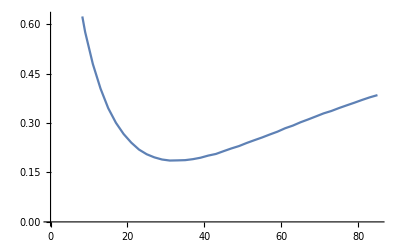
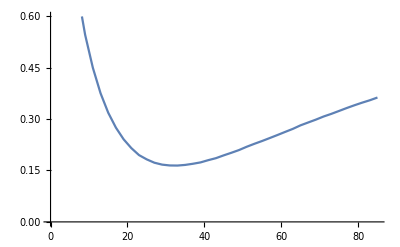
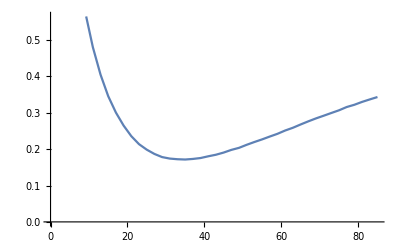
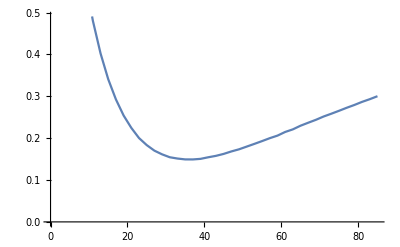
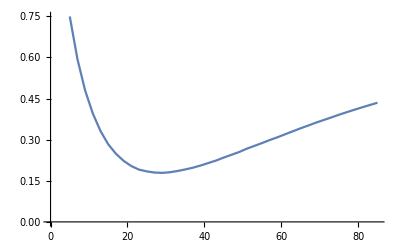
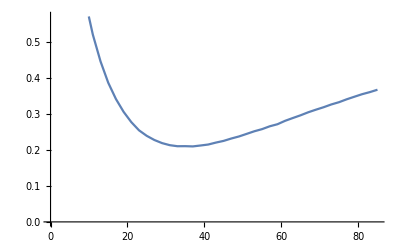
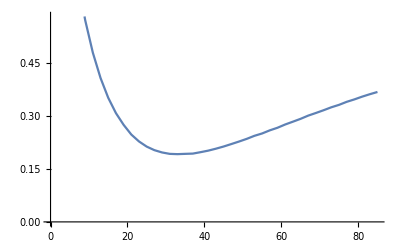
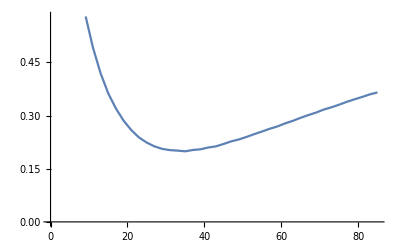

```mathematica
Table[ListLinePlot[Misfit[2.9,0,n]],{n,10}]
```

```mathematica
Table[ListLinePlot[Misfit[2.9,0,n]],{n,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["~/PhD_new/PhD/sub_example.dat",%56[[3]]]
```

~/PhD_new/PhD/sub_example.dat

```mathematica
Export["~/PhD_new/PhD/without_sub_example.dat",%119[[3]]]
```

~/PhD_new/PhD/without_sub_example.dat

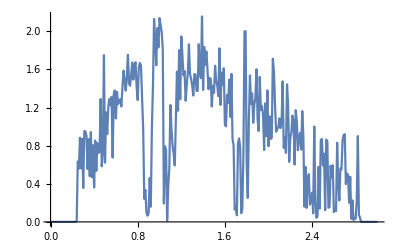

```mathematica
%119[[3]]//ListLinePlot
```